```mathematica
vel:=1
lado:=1
theta:=Pi/3
pos:={lado/2,lado/2}
mode[A_,B_,m_,n_,t_,xpos_,ypos_]:=(A*Cos[vel*Pi*Sqrt[m*m+n*n]*t/lado]+B*Sin[vel*Pi*Sqrt[m*m+n*n]*t/lado])Sin[m*Pi*xpos/lado]*Sin[n*Pi*ypos/lado]
wave[t_,xpos_,ypos_]:=mode[0.1,0.1,1,1,t,xpos,ypos]+mode[0.1,0.1,2,2,t,xpos,ypos]
y[a_,b_,th_]:=2*Cos[b]*Cos[b]*Cos[th+a]*Cos[a]/(1-Sin[a]*Sin[a]*Sin[b]*Sin[b]) -Cos[th]
x[a_,b_,th_]:=-2*Sin[b]*Cos[b]*Cos[th+a]*Cos[a]/(1-Sin[a]*Sin[a]*Sin[b]*Sin[b])
corr[t_]:=NSolveValues[wave[t,x,pos[[2]]]==x*Tan[Pi/2-theta]-pos[[1]],x,Reals]
alpha[t_]:=ArcTan[D[wave[t,xpos,pos[[2]]],xpos] /.xpos->corr[t][[1]]]
beta[t_]:=ArcTan[D[wave[t,corr[t][[1]],ypos],ypos]/.ypos->pos[[2]]]
```

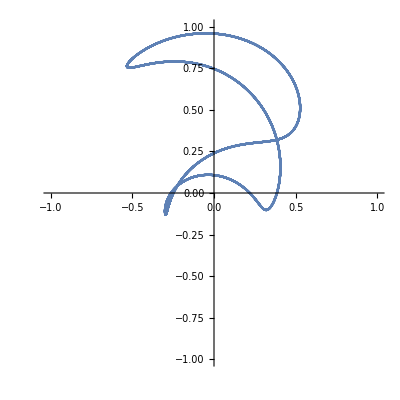

```mathematica
ParametricPlot[{x[alpha[t],beta[t],theta],y[alpha[t],beta[t],theta]},{t,0,10},PlotRange->{{-1,1},{-1,1}},AspectRatio->Full]
```